Show the Importpaclet:ref/Import elements available in this file:

```mathematica
Import["ExampleData/mathematica.pdf", "Elements"]
```

{Author,CreationDate,Creator,PageCount,Pages,Plaintext,Title}

Extract raw text from a PDF file:

```mathematica
Import["ExampleData/mathematica.pdf", "Plaintext"]
```

Mathematica

Import three meta-information elements:

```mathematica
Import["ExampleData/mathematica.pdf",{{"Title", "Creator", "CreationDate"}}]
```

{PDF Sample File,Mac OS X 10.4.8 Quartz PDFContext,Thu 18 Jan 2007 16:09:21}

```mathematica
Import["C:\\Users\\Alison\\Desktop\\2015_Hobbs&Ord_TheBook.pdf","Elements"]
```

{Attachments,Author,CreationDate,Creator,Images,Keywords,PageCount,Pages,Plaintext,RawAttachments,Subject,Title}

```mathematica
Import["C:\\Users\\Alison\\Desktop\\2015_Hobbs&Ord_TheBook.pdf","Plaintext"]
```

1859884
 |  |  |  |

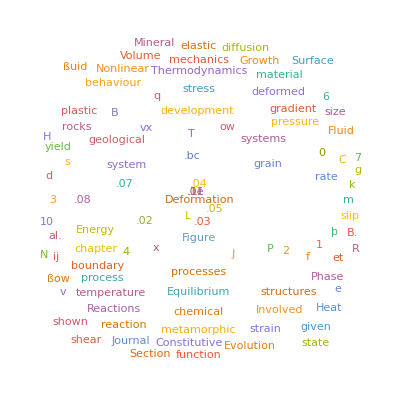

```mathematica
WordCloud[%]
```